# Distance of Function

```mathematica
h[x_]:=5.2551(x-5)^0.7+27
```

```mathematica
D[h[x],x]
```

3.67857/(-5+x)^0.3

```mathematica
dh[x_]:=3.6785699999999997/(-5+x)^0.3000000000000000
```

```mathematica
sol=Flatten[Table[{{x1,y1},x/.NSolve[x+h[x]dh[x]==dh[x]y1+x1,x][[1]]},{x1,8,200,4},{y1,28,200,4}],1];
```

```mathematica
ksol=Interpolation[sol]
```

InterpolatingFunction[{{8.,200.},{28.,200.}},<>]

```mathematica
Normal[Series[ksol[x,y],{x,30,20},{y,70,20}]]
```

26.68+0.323557 (-30+x)+0.00145497 (-30+x)^2-1.5618×10^-6 (-30+x)^3+(0.472945+0.00213763 (-30+x)-0.0000148779 (-30+x)^2+8.5844×10^-9 (-30+x)^3) (-70+y)+(0.0000156193-0.0000197892 (-30+x)+1.88021×10^-7 (-30+x)^2+1.3816×10^-10 (-30+x)^3) (-70+y)^2+(-1.81285×10^-6+2.2826×10^-7 (-30+x)-2.67754×10^-9 (-30+x)^2-5.70839×10^-12 (-30+x)^3) (-70+y)^3

```mathematica
ksol10[x_,y_]:=33.71892354530993+0.3795293817219242 (-50+x)+0.0013354459124487739 (-50+x)^2-2.31241871276322*^-6 (-50+x)^3+(0.5098867414348195+0.0015673596165745075 (-50+x)-0.000013301396103943333 (-50+x)^2+3.908274530308592*^-8 (-50+x)^3) (-70+y)+(-0.0003058829061108729-0.000012512980890486209 (-50+x)+1.6665451451974248*^-7 (-50+x)^2-6.966027442198318*^-10 (-50+x)^3) (-70+y)^2+(1.6839890400394738*^-6+1.2401449366888887*^-7 (-50+x)-2.3266681020510903*^-9 (-50+x)^2+1.3339618951185964*^-11 (-50+x)^3) (-70+y)^3
```

```mathematica
Dist[x_,y_]:=√((x-ksol[x,y])^2+(y-h[ksol[x,y]])^2)
Dist10[x_,y_]:=√((x-ksol10[x,y])^2+(y-h[ksol10[x,y]])^2)
```

```mathematica
Plot3D[ksol[x,y]-ksol10[x,y],{x,8,100},{y,28,150},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Dist[x,y]-Dist10[x,y],{x,8,100},{y,28,150},PlotRange->All]
```

-Graphics3D-

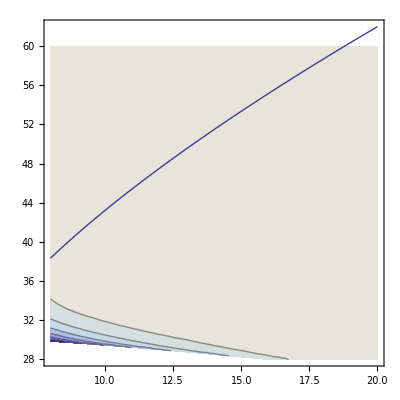

```mathematica
Show[
ContourPlot[Dist[x,y]-Dist10[x,y],{x,8,20},{y,28,60},PlotRange->All],
Plot[5.2551(x-5)^0.7+27,{x,8,20}]
]
```

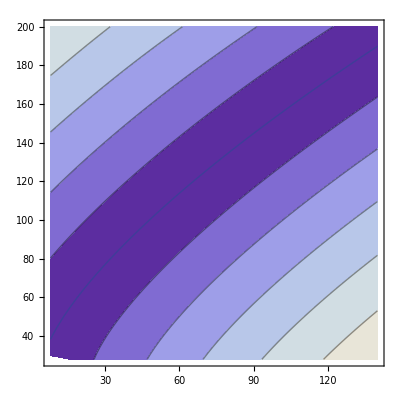

```mathematica
Show[
ContourPlot[Dist10[x,y],{x,8,140},{y,28,200}],
Plot[5.2551(x-5)^0.7+27,{x,8,140}]
]
```

```mathematica
Plot3D[Dist10[x,y],{x,8,140},{y,28,200}]
```

-Graphics3D-